```mathematica
data= Import["/Users/yangm/Desktop/Sum_Eigenvalues.xlsx"];
data = data[[1]];
k = data[[All,1]];
sum = data[[All,2]];
```

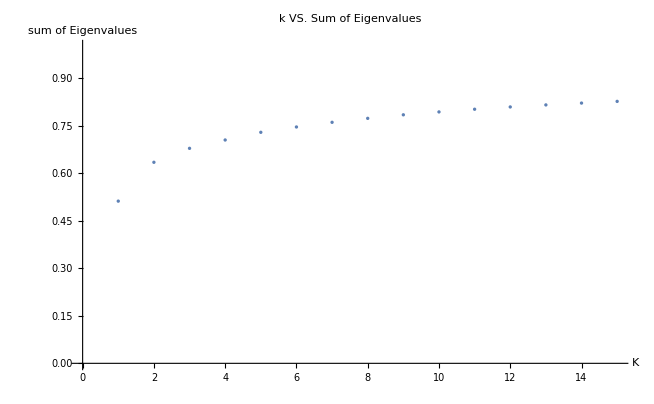

```mathematica
ListPlot[data,PlotLabel->"k VS. Sum of Eigenvalues",AxesLabel->{"K", "sum of Eigenvalues"},LabelStyle->Directive[Blue],PlotRange->{{0,15},{0,1}}]
```

```mathematica
data1= Import["/Users/yangm/Desktop/Eigenvalues.xlsx"];
data1 = data1[[1]];
k1 = data1[[All,1]];
sum1 = data1[[All,2]];
```

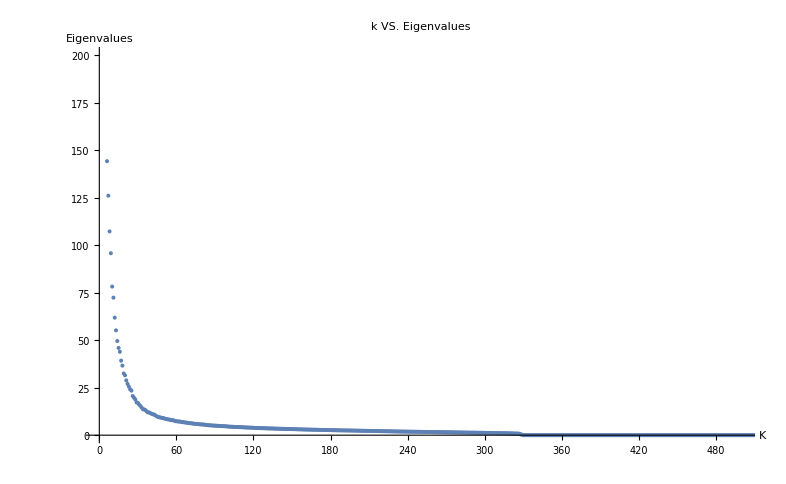

```mathematica
ListPlot[data1,PlotLabel->"k VS. Eigenvalues",AxesLabel->{"K", "Eigenvalues"},LabelStyle->Directive[Blue],PlotRange->{{0,500},{0,200}}]
```